```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["SMatrix`", Path->ParentDirectory@NotebookDirectory[]]
Directory[]
```

C:\Users\marucha\Desktop\SMatrixBootstrap\pionScatteringResult

```mathematica
resultDirectories = FileNames["*_out"]
```

{cubic_coupling_n_12_j_24.max.gz_out,cubic_coupling_n_14_j_26.max.gz_out,cubic_coupling_n_16_j_28.max.gz_out,cubic_coupling_n_18_j_30.max.gz_out,cubic_coupling_n_4_j_16.max.gz_out,cubic_coupling_n_8_j_20.max.gz_out,quartic_coupling_imp_n_0_j_8.max.gz_out,quartic_coupling_imp_n_0_j_8.min.gz_out,quartic_coupling_imp_n_10_j_22.max.gz_out,quartic_coupling_imp_n_10_j_22.min.gz_out,quartic_coupling_imp_n_12_j_24.max.gz_out,quartic_coupling_imp_n_12_j_24.min.gz_out,quartic_coupling_imp_n_14_j_26.max.gz_out,quartic_coupling_imp_n_14_j_26.min.gz_out,quartic_coupling_imp_n_16_j_28.max.gz_out,quartic_coupling_imp_n_16_j_28.min.gz_out,quartic_coupling_imp_n_18_j_30.max.gz_out,quartic_coupling_imp_n_18_j_30.min.gz_out,quartic_coupling_imp_n_1_j_9.max.gz_out,quartic_coupling_imp_n_1_j_9.min.gz_out,quartic_coupling_imp_n_20_j_32.max.gz_out,quartic_coupling_imp_n_20_j_32.min.gz_out,quartic_coupling_imp_n_2_j_10.max.gz_out,quartic_coupling_imp_n_2_j_10.min.gz_out,quartic_coupling_imp_n_3_j_11.max.gz_out,quartic_coupling_imp_n_3_j_11.min.gz_out,quartic_coupling_imp_n_4_j_16.max.gz_out,quartic_coupling_imp_n_4_j_16.min.gz_out,quartic_coupling_imp_n_6_j_18.max.gz_out,quartic_coupling_imp_n_6_j_18.min.gz_out,quartic_coupling_imp_n_8_j_20.max.gz_out,quartic_coupling_imp_n_8_j_20.min.gz_out,quartic_coupling_n_10_j_20.max.gz_out,quartic_coupling_n_10_j_20.min.gz_out,quartic_coupling_n_10_j_22.max.gz_out,quartic_coupling_n_10_j_22.min.gz_out,quartic_coupling_n_12_j_24.max.gz_out,quartic_coupling_n_12_j_24.min.gz_out,quartic_coupling_n_14_j_26.max.gz_out,quartic_coupling_n_14_j_26.min.gz_out,quartic_coupling_n_16_j_28.max.gz_out,quartic_coupling_n_16_j_28.min.gz_out,quartic_coupling_n_18_j_30.max.gz_out,quartic_coupling_n_18_j_30.min.gz_out,quartic_coupling_n_8_j_20.max.gz_out,quartic_coupling_n_8_j_20.min.gz_out,quartic_coupling_with_pole_n_10_j_22.max.gz_out,quartic_coupling_with_pole_n_10_j_22.min.gz_out,quartic_coupling_with_pole_n_12_j_24.max.gz_out,quartic_coupling_with_pole_n_12_j_24.min.gz_out,quartic_coupling_with_pole_n_14_j_26.max.gz_out,quartic_coupling_with_pole_n_14_j_26.min.gz_out,quartic_coupling_with_pole_n_16_j_28.max.gz_out,quartic_coupling_with_pole_n_16_j_28.min.gz_out,quartic_coupling_with_pole_n_18_j_30.max.gz_out,quartic_coupling_with_pole_n_18_j_30.min.gz_out,quartic_coupling_with_pole_n_4_j_16.max.gz_out,quartic_coupling_with_pole_n_4_j_16.min.gz_out}

```mathematica
ParseFilename[name_]:=  StringCases[name,
"quartic_coupling_"~~variation:Longest[("imp_"|"with_pole_"|"")]~~"n_"~~n:NumberString~~"_j_"~~j:NumberString~~"."~~type:("max"|"min")~~".gz_out":><|"variation"->variation,"type"->type,"n"->ToExpression[n],"j"->ToExpression[j]|>]//First
```

```mathematica
LoadResults[directory_]:= Module[{keyfile = StringDrop[directory,-10]<>"key.m"},
Join[ParseFilename[directory],LoadSDPBOutput[directory, keyfile]]
];
```

```mathematica
dataset = Select[KeyExistsQ["primalObjective"]][LoadResults/@resultDirectories]//Select[#terminateReason=="found primal-dual optimal solution"&]//Quiet; Dataset[dataset]
```

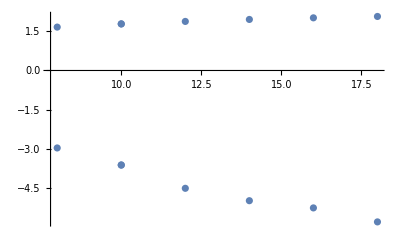

```mathematica
Map[{#n,1/(32π)#vector[α[0,0,0]]}&,Select[dataset,#variation==""&]]//ListPlot
```

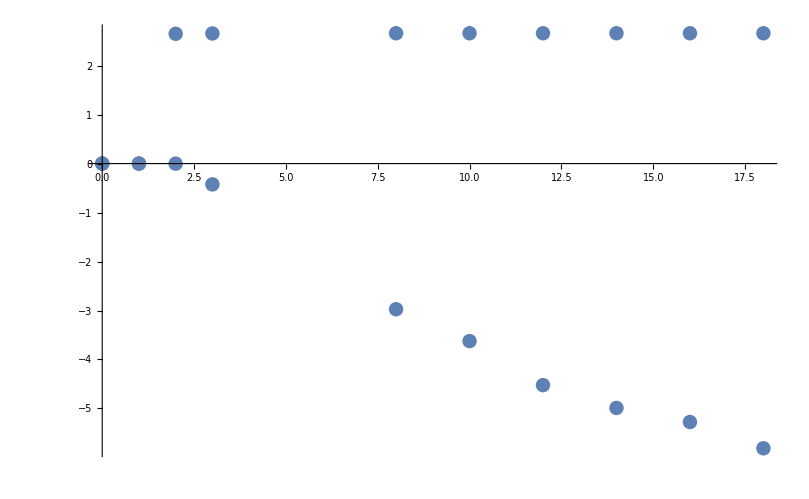

```mathematica
Map[{#n,1/(32π)#vector[α[0,0,0]]}&,Select[dataset,#variation=="imp_"&]]//ListPlot
```

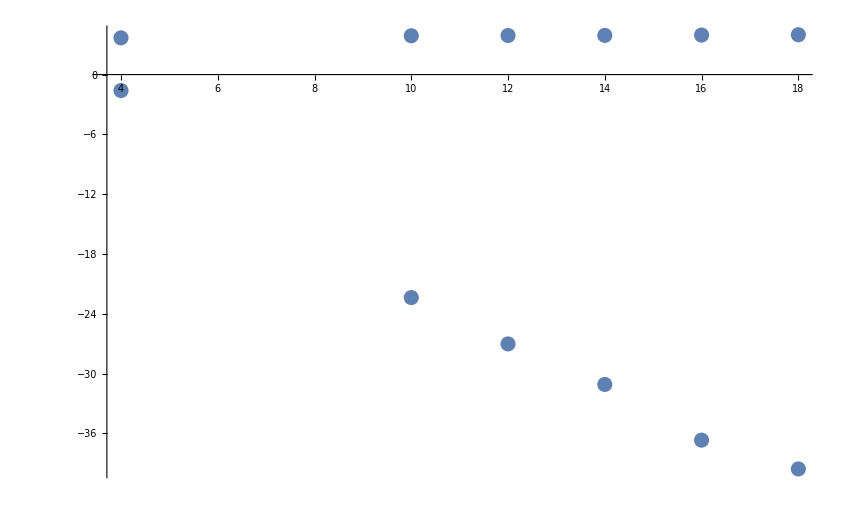

```mathematica
Map[{#n,1/(32π)#vector[α[0,0,0]]}&,Select[dataset,#variation=="with_pole_"&]]//ListPlot
```